# Projekt za Računalniška orodja v matematiki

24.6.2022

## Podatki, ki jih bomo uporabili

```mathematica
drzave=EntityList["Country"];
```

Povprečne mesečne, sezonske in pa letne temperature. (To bom dopolnil še kasneje.)

Uvozil bom podatke iz excela, ki povedo kolikšna je letna anomalija na svetovnem merilu glede na povprečje 20. stoletja, pridobljeni so pa na:

```mathematica
Hyperlink["https://www.ncdc.noaa.gov/cag/global/time-series/globe/land_ocean/ann/2/1880-2021"]
```

https://www.ncdc.noaa.gov/cag/global/time-series/globe/land_ocean/ann/2/1880-2021

```mathematica
Hyperlink["https://pxweb.stat.si/SiStatData/pxweb/sl/Data/-/0156101S.px/table/tableViewLayout2/"]
```

https://pxweb.stat.si/SiStatData/pxweb/sl/Data/-/0156101S.px/table/tableViewLayout2/

```mathematica
podatkiIzExcela = Import["C:\\Users\\ALEN\\Desktop\\FMF\\1. Letnik\\ROM\\Projekt_ROM_github\\globalne_temperature.csv", "Dataset"];
```

```mathematica
podatkiOSloveniji = Import["C:\\Users\\ALEN\\Desktop\\FMF\\1. Letnik\\ROM\\Projekt_ROM_github\\slo_temperature.csv","Dataset","FieldSeperators"-> ";"];
```

```mathematica
podatkiIzExcelaVTabeli = podatkiIzExcela[[6;;All ]] //TableForm;
```

```mathematica
podatkiOSlovenijiVTabeli = podatkiOSloveniji[[4;;All ]]//TableForm;
```

## Globalno

```mathematica
seznamAnomalijTemperatur=Table[podatkiIzExcelaVTabeli[[1]][[i]][[2]],{i,1,Length[podatkiIzExcelaVTabeli[[1]]]}];
```

Prikaz anomalij globalne temperature od leta 1880 do leta 2020.

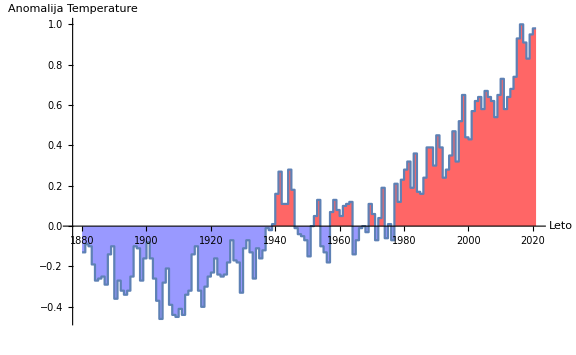

```mathematica
ListStepPlot[{seznamAnomalijTemperatur},DataRange->{1880, 2020},ImageSize->Large,AxesLabel->{"Leto","Anomalija Temperature"},Filling->Axis,FillingStyle->{Opacity[0.4,Blue], Opacity[0.6,Red]}]
```

## Slovenija

Poglejmo letne povprečne temperature za Slovenijo med leti 2001 in 2014.

```mathematica
seznamPovprecnihTemperaturLeto =Table[2001 + i, {i,0, 13}]
```

{2001,2002,2003,2004,2005,2006,2007,2008,2009,2010,2011,2012,2013,2014}

```mathematica
seznamPovprecnihTemperaturStevilke = {9.3,9.8,9.5,8.6,8.3,9.1,9.7,9.4,9.4,8.5,9.5,9.7,9.3,10.3}
```

{9.3,9.8,9.5,8.6,8.3,9.1,9.7,9.4,9.4,8.5,9.5,9.7,9.3,10.3}

```mathematica
koordinate = MapThread[{#1,#2}&,{seznamPovprecnihTemperaturLeto,seznamPovprecnihTemperaturStevilke}]
```

{{2001,9.3},{2002,9.8},{2003,9.5},{2004,8.6},{2005,8.3},{2006,9.1},{2007,9.7},{2008,9.4},{2009,9.4},{2010,8.5},{2011,9.5},{2012,9.7},{2013,9.3},{2014,10.3}}

```mathematica
najboljsaPremica = LinearModelFit[koordinate,x,x];
```

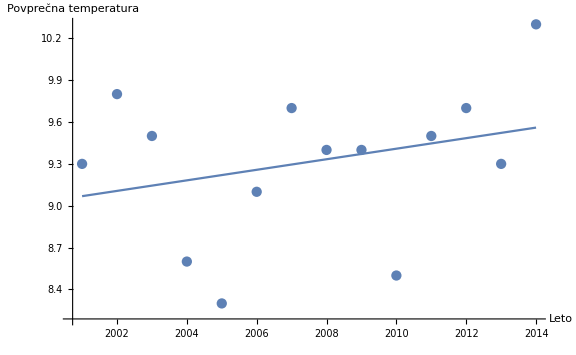

```mathematica
Show[ListPlot[koordinate,LabelingFunction->Tooltip,ImageSize->Large,DataRange->{2001,2014},AxesLabel->{"Leto","Povprečna temperatura"}],
Plot[najboljsaPremica["BestFit"], {x,2001,2014}]]
```

Vidimo, da naša regresijska premica narašča. Iz tega lahko sklepamo, da se letne povprečne temperature v Sloveniji s vsakim letom povečujejo.

## Aplikacija v oblaku

```mathematica
Graf[mesto_]:=DateListPlot[WeatherData[mesto,"Temperature",{{1950,1,1},{2021,12,12},"Year"}],Joined->True]
```

```mathematica
obrazec=FormPage["mesto"->"City",Graf[#mesto]&,AppearanceRules-><|"Title"->"Graf temperature med letih 1950 in 2022 za določeno mesto",
				"Description"->"Vnesi ime mesta","SubmitLabel"->"Potrdi"|>];
```

```mathematica
CloudDeploy[obrazec,Permissions->"Public"]
```

CloudObject[https://www.wolframcloud.com/obj/9b724fe5-1ff0-44c3-ae8e-759ea7260e87]